{1,2,3,4}

( | 1 | 2 | 3 | 4
1 | 1 | 1 | 1 | 0
2 | 1 | 0 | 0 | 0
3 | 0 | 0 | 1 | 1
4 | 0 | 1 | 0 | 1)

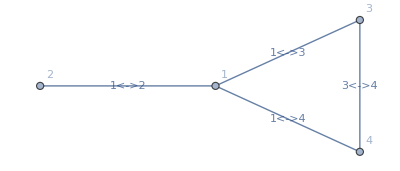

```mathematica
ClearAll["Global`*"]
(*----------2 Rewireing Networks----------*)
(*----------Basic Setup----------*)
n=4;


(*----------Distance Matrice between the nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
m[[2,3]]=0; m[[1,3]]=1;

tablelabel=Table[x,{x,n}]
MatrixForm[m, TableHeadings->{tablelabel,tablelabel}]

IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"]

(*----------Average Path Length Calculation----------*)
apl=sumDist/(n*(n-1));

(*----------Output----------*)


apl;
```